# Lecture 31: SVD Algorithms

Time to learn how to compute the SVD A=U.Σ.V^*.  Not surprisingly, SVD algorithms look like eigenvalue algorithms.

## Eigenvalues of A^*.A

If A=U.Σ.V^* is the SVD then A^*.A=(U.Σ.V^*)^*.U.Σ.V^*=V.Σ^*.U^*.U.Σ.V^*=V.Σ^*.Σ.V^* since U is unitary.  More over, since Σ is real we wind up with A^*.A=V.Σ^2.V^*.  We can compute the Hermitian eigenvalue problem A^*.A=V.Λ.V^* then compute 
Σ as the diagonal matrix of the positive square roots of Λ and compute U from U.Σ=A.V.  The problem with this (or similarly computing with A.A^*) is that we know this problem (just like the normal equations) is more sensitive to perturbations than it needs to be.   The fundamental problem is the we formed the product. The stability problem is most extreme for the smaller singular values.

Just another reminder why forming A.A^* is a bad idea. I am going to make a matrix with a broad range of singular values.  The BuiltIn SVD does almost OK with the following

```mathematica
{m,n}={18,17};
σsIn=Sort[Table[10.0^(i-8),{i,Min[m,n]}]]
S=SparseArray[Band[{1,1}]->σsIn,{m,n}];
U=Orthogonalize[RandomReal[{-1,1},{m,m}]];
V=Orthogonalize[RandomReal[{-1,1},{n,n}]];
A=U.S.Vᵀ;
σsBIOut=Sort[SingularValueList[A,Tolerance->0]];
(σsBIOut-σsIn)/σsIn
```

{1.×10^-7,1.×10^-6,0.00001,0.0001,0.001,0.01,0.1,1.,10.,100.,1000.,10000.,100000.,1.×10^6,1.×10^7,1.×10^8,1.×10^9}

{0.0232488,-0.00337242,0.000687709,-0.0000370585,-1.35683×10^-6,1.19079×10^-6,2.43819×10^-8,-1.01962×10^-8,1.2019×10^-10,5.72109×10^-11,-1.00283×10^-11,2.36287×10^-13,-1.02591×10^-13,2.01399×10^-14,-1.11759×10^-15,-1.49012×10^-16,0.}

The A.A^* computation is completely broken!

```mathematica
Sqrt[Eigenvalues[A.ConjugateTranspose[A]]]
```

{1.×10^9,1.×10^8,1.×10^7,1.×10^6,100000.,10000.,999.981,100.016,0.+15.4476 ⅈ,9.72002,5.91845,0.+5.38333 ⅈ,4.6125,0.+2.85906 ⅈ,2.59147,1.93908,0.+1.14175 ⅈ,0.+0.229136 ⅈ}

```mathematica
Sqrt[Eigenvalues[ConjugateTranspose[A].A]]
```

{1.×10^9,1.×10^8,1.×10^7,1.×10^6,100000.,10000.,1000.,99.9026,10.356,6.57393,0.+6.15052 ⅈ,0.+4.93748 ⅈ,0.+3.98468 ⅈ,2.83247,0.+1.96651 ⅈ,1.60959,0.+0.581897 ⅈ}

## Eigenvalues of H=(0 | A^* A | 0)

A direct computation shows that if A=U.Σ.V^* then 
	(0 | A^*
A | 0).(V | V
U | -U)=(A^*.U | -A^*.U
A.V | A.V)
Since A=U.Σ.V^* we have A.V=U.Σ.V^*.V=U.Σ.  
Since A^*=V.Σ.U^* we have that A^*.U=V.Σ.U^*.U=V.Σ. 
So
	(0 | A^*
A | 0).(V | V
U | -U)=(V.Σ | -V.Σ
U.Σ | U.Σ)=(V | V
U | -U).(Σ | 0
0 | -Σ).
In words, the eigen values of the big Hermitian matrix in the heading are ± the singular values. The singular vectors are in the eigenvectors.

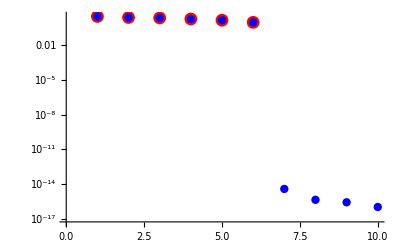

```mathematica
{m,n}={14,6};
A=RandomReal[{-1,1},{m,n}];
H=ArrayFlatten[({{0, ConjugateTranspose[A]}, {A, 0}})];
MatrixPlot[H];
{λ,V}=Eigensystem[H];
σ=SingularValueList[A];
ListLogPlot[{σ,Select[λ,Positive]},GridLines->Automatic,
PlotStyle->{
Directive[Red,PointSize[0.023]],
Directive[Blue, PointSize[0.015]]}]
```

```mathematica
λ
```

{3.12656,-3.12656,-2.55788,2.55788,2.34196,-2.34196,1.89539,-1.89539,1.48123,-1.48123,0.973546,-0.973546,3.84542×10^-15,4.4092×10^-16,2.68621×10^-16,-1.31998×10^-16,-1.29141×10^-16,1.0543×10^-16,-4.79748×10^-18,-1.93285×10^-18}

This stable algorithm is what computes 99.999% of all SVDs in the world.  The implementation is sneaky because it does not actually need to make the big H matrix! Just like for eigenvalues there is a preliminary reduction.

For singular values, we can get to an upper bi-diagonal matrix! The bi-diagonal form is then iteratively reduced to a diagonal form.  If you only want singular values you do not need to keep the rotations

### Bi-diagonalization: Golub Kahan

The plan is to use separate Householder operations on the left and right to rotate the matrix to an upper bi-diagonal form. I am going to call the right rotations U and the left rotations V.

```mathematica
{m,n}={24,5};
A=RandomReal[{-1,1},{m,n}];
R=QRDecomposition[A][[2]];
Map[SingularValueList,{A,R,Rᵀ}]ᵀ

Map[MatrixPlot,{A,R}];
```

{{3.87787,3.87787,3.87787},{2.97732,2.97732,2.97732},{2.69741,2.69741,2.69741},{2.31279,2.31279,2.31279},{1.90087,1.90087,1.90087}}

#### Preliminary Script.

```mathematica
SetOptions[MatrixPlot,ColorRules->{0->Green}, Mesh->All];
{m,n}={10,4};
A=A0=RandomReal[{-1,1},{m,n}];
U=HouseMat[A⟦1;;m,1⟧];
A⟦1;;m,1;;n⟧=Chop[U.A⟦1;;m,1;;n⟧];
Pic1=MatrixPlot[A];
V=HouseMat[A⟦1,2;;n⟧];
A⟦1;;m,2;;n⟧=Chop[A⟦1;;m,2;;n⟧.V];
Pic2=MatrixPlot[A];
U=HouseMat[A⟦2;;m,2⟧];
A⟦2;;m,2;;n⟧=Chop[U.A⟦2;;m,2;;n⟧];
Pic3=MatrixPlot[A];
V=HouseMat[A⟦2,3;;n⟧];
A⟦2;;m,3;;n⟧=Chop[A⟦2;;m,3;;n⟧.V];
Pic4=MatrixPlot[A];
U=HouseMat[A⟦3;;m,3⟧];
A⟦3;;m,3;;n⟧=Chop[U.A⟦3;;m,3;;n⟧];
Pic5=MatrixPlot[A];
V=HouseMat[A⟦3,4;;n⟧];
A⟦3;;m,4;;n⟧=Chop[A⟦3;;m,4;;n⟧.V];
Pic6=MatrixPlot[A];
U=HouseMat[A⟦4;;m,4⟧];
A⟦4;;m,4;;n⟧=Chop[U.A⟦4;;m,4;;n⟧];
Pic7=MatrixPlot[A];
TabView[{Pic1,Pic2,Pic3,Pic4,Pic5,Pic6,Pic7}]
```

1234567

I guess we should check that the singular values are being preserved.

```mathematica
TableForm[Map[SingularValueList,{A,A0}]]
```

2.36711 | 1.9143 | 1.45805 | 1.17622
2.36711 | 1.9143 | 1.45805 | 1.17622

#### Function Golub-Kahan

```mathematica
GKBiDiagonalization[AIn_]:= Module[{A=AIn,m,n,U,V},
{m,n}=Dimensions[AIn];
(* Assuming Tall Skinny m≥n *) 
Do[
U=HouseMat[A⟦k;;m,k⟧];
A⟦k;;m,k;;n⟧=Chop[U.A⟦k;;m,k;;n⟧];
V=HouseMat[A⟦k,k+1;;n⟧];
A⟦k;;m,k+1;;n⟧=Chop[A⟦k;;m,k+1;;n⟧.V],
{k, 1,n-1}];
(* Tidy up the Last Column *)
U=HouseMat[A⟦n;;m,n⟧];
A⟦n;;m,n;;n⟧=Chop[U.A⟦n;;m,n;;n⟧];
A]
```

{{4.04298,3.47806,2.90311,2.83225,2.29178,1.69883,1.37624},{4.04298,3.47806,2.90311,2.83225,2.29178,1.69883,1.37624}}

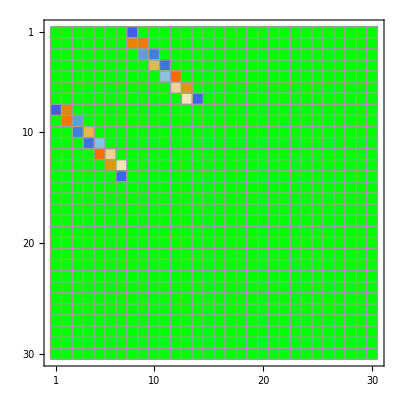

```mathematica
{m,n}={23,7};
A=RandomReal[{-1,1},{m,n}];
B=GKBiDiagonalization[A];
H=ArrayFlatten[({{0, ConjugateTranspose[B]}, {B, 0}})];
Map[SingularValueList,{A,B}]
MatrixPlot[H]
```

### Bi-diagonalization: Lawson Hanson Chan

An alternative would be to Upper Triangularize using QR then Bidiaogonalize the remaining Upper Triangle just like above.

#### Function Lawson-Hanson-Chan

```mathematica
LHCBiDiagonalization[A_]:= Module[{R,m,n,U,V},
{m,n}=Dimensions[A];
(* Assuming Tall Skinny m≥n *)
R=QRDecomposition[A]⟦2⟧;
R=GKBiDiagonalization[R]; 
ArrayFlatten[ ({{R}, {ConstantArray[0,{m-n,n}]}})]
]
```

{{3.83552,3.64974,2.72411,2.70236,2.48656,2.12499,1.06254},{3.83552,3.64974,2.72411,2.70236,2.48656,2.12499,1.06254}}

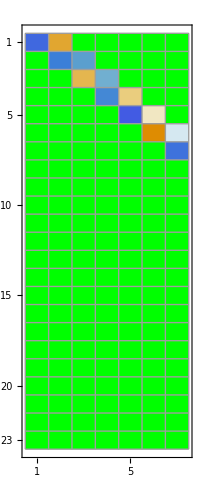

```mathematica
A=RandomReal[{-1,1},{m,n}];
B=LHCBiDiagonalization[A];
Map[SingularValueList,{A,B}]
MatrixPlot[B]
```

### Operation Counts and Three Step BiDiagonalization

It turns out that LHC is more work than GK for nearly square matrices. While GK is more work for very tall skinny matrices. So the right thing to do depends on the aspect ratio γ=m/n

GK 	~4 m n^2-4/3 n^3=4/3 n^3 (3γ-1)

LHC	~2 m n^2+2 n^3=2 n^3 (γ+1)

To find the crossover point solve 4/3 n^3 (3γ-1)=2n^3(γ+1) for γ.

The crossover point is γ=m/n=5/3: LHC is less work above 5/3 and GK is less work below 5/3.

Just to make it a little more complicated as far as operation counts are concerned

Do GK at the beginning if it is better

Run down the diagonal and and switch to the LHC code once it becomes cost effective.

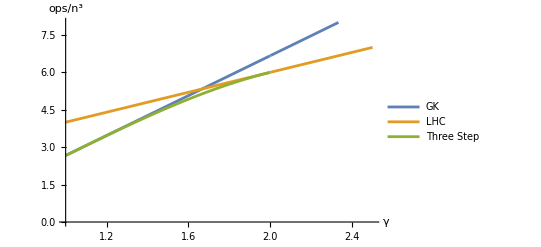

```mathematica
Plot[ {4/3*(3γ-1),2(γ +1),If[γ<2,2/3*(3 γ+3 γ^2-γ^3-1)]},{γ,1,2.5},
PlotRange->{0,8},GridLines->{{5/3,2},None},
PlotLegends->{"GK","LHC","Three Step"},AxesLabel->{"γ","ops/n^3"}]
Clear[m,n,γ]
Simplify[(4 m n^2-4/3 n^3)/.m->γ n];
Simplify[(2 m n^2+2 n^3)/.m->γ n];
Simplify[(4 m n^2-4/3 n^3-2/3(m-n)^3)/.m->γ n];
```

## From Lecture 10: Householder Reflection Code

### Householder Reflections Matrix Functions

If v is a unit vector parallel to 
	sign(a⟦1⟧)||a||e_1+a
then the orthogonal matrix Q=I-2 v⊗v satisfies
	Q.a=||a||e_1
In other words, Q rotates the vector a to align with the vector e_1.

```mathematica
HouseVec[a_]:= Module[{v=a},
v⟦1⟧+=Sign[a⟦1⟧]Norm[a];
v/Norm[v]]
HouseMat[a_]:= Module[{v},
v=HouseVec[a];
IdentityMatrix[Length[a]]-2 KroneckerProduct[v,v]]
```

```mathematica
m=21;
a=RandomReal[{-1,1},m];
Q=HouseMat[a];
Norm[Q.Qᵀ -IdentityMatrix[m]]
Chop[Q.a]
```

4.46272×10^-16

{2.88227,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### Householder Reflections Action Functions

There is no need to build the Householder matrix.  All we need to be able to do is apply the matrix to a vector x.

```mathematica
HouseActionVec[x_,a_]:= Module[{v},
v=HouseVec[a];
x-2 v (v.x)]
```

As always TEST!

```mathematica
m=14;
{x,a}=RandomReal[{-1,1},{2,m}];
Q=HouseMat[a];
Map[Norm,{Q.x-HouseActionVec[x,a],Q.a- HouseActionVec[a,a]}]
```

{3.97399×10^-16,1.12638×10^-15}